```mathematica
SetDirectory[NotebookDirectory[]] ;
```

```mathematica
data = Import["solution.dat"];
```

```mathematica
Length@data
```

30

```mathematica
i=0;j=0;
For[i=1,i<=Length@data,++i,
For[j=1,j<Length@data[[i]],j++,
data[[i,j]]={data[[i,j]],data[[i,Length@data[[i]]]]};
];
data[[i]]=Delete[data[[i]],Length@data[[i]]];
];
```

```mathematica
data=data[[2;;]];
```

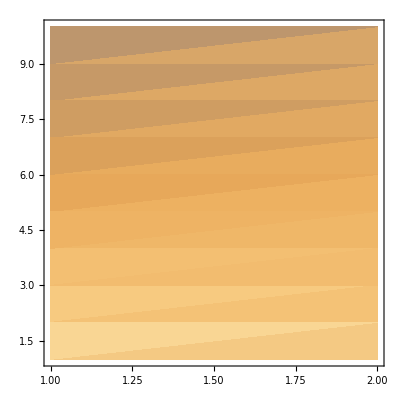

```mathematica
ListDensityPlot[data(*,PlotRange->{{0.5,1.5},{0,1}}*)]
```